### We consider metric d(x,y)=ϕ(|x-y|) on R, and measure μ=1/2(δ_-1+δ_1) on R. The function f computes f(x) = ∫d^2(x,y)ⅆμ(y) and we then plot it on interval [-4,4] with red points on all integral points. Find more subadditive function examples, https://core.ac.uk/download/pdf/215258479.pdf

### Let us first plot our ϕ, note that |sin(x)| is a subadditive function,

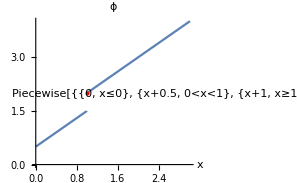

```mathematica
ϕ[x_]:=Piecewise[{{0, x<=0}, {x+0.5, 0<x<1}, {x+1, x ≥1}}];
Plot[ϕ[x],{x,0,3},ClippingStyle->None,AxesOrigin->{0,0},
 Epilog->{Text[Style[TraditionalForm[ϕ[x]],Medium],{2.5,2}],
White,Thickness[0.006],Line[{{1,1.5},{1,2}}],Red,PointSize[Large],Point[{{1,2}}]},AxesLabel->Automatic, PlotLabel->ϕ]
```

### Then we plot function f, whose minimum value corresponds to a barycenter of μ

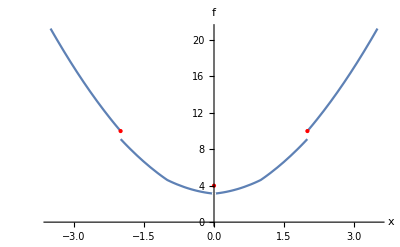

```mathematica
μ=TransformedDistribution[2y-1,y\[Distributed]BernoulliDistribution[0.5]];
f[x_]:=Expectation[ϕ[Abs[y-x]]^2,y\[Distributed]μ];
Plot[f[x], {x,-3.5,3.5},AxesOrigin->{0,0},AxesLabel->Automatic,PlotLabel->f,
Epilog->{PointSize[Large],Red,Point[{#,f[#]}&/@{-2,0,2}],White,Point[{{0,3.125}}]}]
```